```mathematica
Needs["gUtils`"];
Needs["gBRDF`"];

(*https://math.libretexts.org/Courses/Monroe_Community_College/MTH_212_Calculus_III/Chapter_14%3A_Multiple_Integration/14.7%3A_Change_of_Variables_in_Multiple_Integrals_(Jacobians)*)
ClearAll[funcX,x,x0,x1,funcU,u,u0,u1,dx,du];
funcX=x(x^2-4)^5;
x0=2;
x1=3;
gPrint["Origin Integral"];
TraditionalForm@HoldForm@Integrate[x(x^2-4)^5,{x,2,3}]
Integrate[funcX,{x,x0,x1}]//N

gPrint["Jacobian Integral"];
u=x^2-4;
gPrint["du"];
du=D[u,x]*dx

ClearAll[u,x,du,dx];
x=Sqrt[u+4];
gPrint["dx"];
dx=D[x,u]*du

gPrint["New integral function"];
funcU=(funcX/.{x->Sqrt[u+4]})*D[x,u]

gPrint["New integral range"];
u0=x0^2-4;
u1=x1^2-4;
{u0,u1}

gPrint["Validating result"];
TraditionalForm@HoldForm@Integrate[u^5/2,{u,0,5}]
Integrate[funcU,{u,u0,u1}]//N

ClearAll[func,x,x0,x1,u,u0,u1,dx,du];
```

Origin Integral

∫_2^3 x (x^2-4)^5ⅆx

1302.08

Jacobian Integral

du

2 dx x

dx

du/(2 √(4+u))

New integral function

u^5/2

New integral range

{0,5}

Validating result

∫_0^5 u^5/2 ⅆu

1302.08

>Jacobian for area differential:

{1., 2.5, 1 + 2 u + v, 2.5}

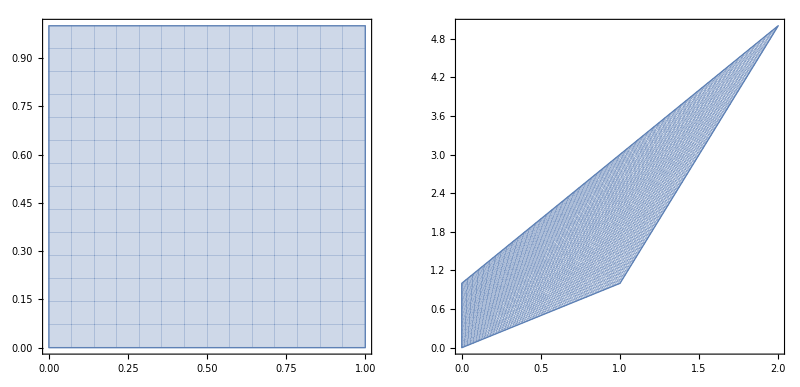

```mathematica
(*https://web.ma.utexas.edu/users/m408s/m408d/CurrentWeb/LM15-10-4.php*)
(*https://math.stackexchange.com/questions/14952/what-is-the-jacobian-matrix*)
ClearAll[x,y,u,v,dxu,dxv,dyu,dyv,jmat,jmat2,jacoDet,areaDiff];

x[u_,v_]:=u+v*u;
y[u_,v_]:=u+v+3u*v;

dxu=D[x[u,v],u];
dxv=D[x[u,v],v];
dyu=D[y[u,v],u];
dyv=D[y[u,v],v];
jmat={{dxu,dxv},{dyu,dyv}};

jmat2=D[{x[u,v],y[u,v]},{{u,v}}];
Assert[jmat==jmat2];
jacoDet=Det[jmat2];
areaDiff=Integrate[jacoDet,{u,0,1},{v,0,1}]//N;

OriginR=Polygon[{{0,0},{0,1},{1,1},{1,0}}];
WarpR=Polygon[{{x[0,0],y[0,0]},{x[0,1],y[0,1]},{x[1,1],y[1,1]},{x[1,0],y[1,0]}}];
gPrint[">Jacobian for area differential:"];
gPrint[ToString@{Area[OriginR]//N,Area[WarpR]//N,ToString[Det[jmat]],areaDiff}];
{ParametricPlot[{u,v},{u,0,1},{v,0,1}],ParametricPlot[{x[u,v],y[u,v]},{u,0,1},{v,0,1}]}//GraphicsRow

ClearAll[x,y,u,v,dxu,dxv,dyu,dyv,jmat,jmat2,jacoDet,areaDiff];
```

```mathematica
(*https://schuttejoe.github.io/post/ggximportancesamplingpart1/*)
ClearAll[x,y,z,r,θ,ϕ,jmat];

x=r*Sin[θ]Cos[ϕ];
y=r*Cos[θ];
z=r*Sin[θ]Sin[ϕ];

jmat=D[{x,y,z},{{r,θ,ϕ}}];
gPrint["Jacobian of the transformation from spherical to Cartesian"];
Print[Style[FullSimplify@Det[jmat],FontSize->18,Background->LightBlue]];

ClearAll[x,y,z,r,θ,ϕ,jmat];
```

Jacobian of the transformation from spherical to Cartesian

-r^2 Sin[θ]

```mathematica
(*Paper: Notes on the Ward BRDF*)
(*https://schuttejoe.github.io/post/ggximportancesamplingpart1/*)
Quiet@ClearAll[Subscript[p, h],po,thetaH,Subscript[θ, h],thetaO,phiH,phiO];

thetaH=thetaO/2;
phiH=phiO;
detH=Det[D[{thetaH,phiH},{{thetaO,phiO}}]];
(*ph/po are probablities on non-Euclidean space/the sphere of directions*)
(*transform the probability in spherical coordinates*)
po=Subscript[p, h]*detH*(Sin[Subscript[θ, h]]/(2*Sin[Subscript[θ, h]]*Cos[Subscript[θ, h]]));
gPrint["Jacobian for reflection vector"];
Print[Style[FullSimplify@po,FontSize->18,Background->LightBlue]];

Quiet@ClearAll[Subscript[p, h],po,thetaH,Subscript[θ, h],thetaO,phiH,phiO];
```

Jacobian for reflection vector

1/4 Sec[θ_h] p_h